### The effective Hamiltonian of the Rabi model

Data are imported from julia code https : // github . com/djuliannader/RabiModel

```mathematica
R=50; (*quibit frequency*)
H[q_,p_]=(q^2+p^2)/2-(1/2)*(1+(Sqrt[2]*g*q+λ)^2)^(1/2);
V[q_,gg_,λλ_]=q^2/2-(1/2)*(1+(Sqrt[2]*gg*q+λλ)^2)^(1/2);
```

#### First column

```mathematica
g=1/2^(1/2); (*coupling*)
rho1={};
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,2}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
rhoinst=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
AppendTo[rho1,{en,Re[rhoinst]}],{en,-0.499,-0.2,0.0001}];
```

```mathematica
datarho={{-24.42505838235548, 0.6971599105424998},
{-22.978597968671373, 0.6856219724536073},
{-21.50974392668985, 0.6760509761245694},
{-20.021565847933044, 0.6679233603447005},
{-18.51642851652634, 0.6608962041051417},
{-16.996210178274655, 0.6547331626589479},
{-15.46243845092786 ,0.6492647770258408},
{-13.916379652385103, 0.6443656378827293},
{-12.359100048449115, 0.6399404937140422},
{-10.791509304760435, 0.6359154105801086},
{-9.214392194596421, 0.6322319329555061},
{-7.628432291832355, 0.6288431038648016},
{-6.034230037120754, 0.6257106785230641},
{-4.432316756932385 ,0.6228031277491014},
{-2.8231657098653926, 0.6200941779560755},
{-1.2072009088810005, 0.617561724224336}};
dataT=Table[{datarho[[i,1]]/R,4π*datarho[[i,2]]},{i,1,12}];
```

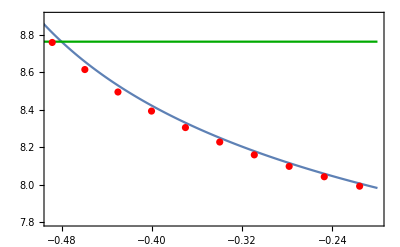

```mathematica
Tc=Show[ListPlot[rho1,Joined->True,GridLines->{{},{}},GridLinesStyle->{{Dashed,Thick},{}},PlotRange->{{-0.49,-0.2},{8.9,7.8}},GridLinesStyle->Red,Frame->True,LabelStyle->{15,Black}],ListPlot[{dataT},PlotStyle->Red],Plot[8.765,{x,-0.5,-0.2},PlotStyle->{Darker[Green]}],Axes->False]
```

#### Second Column

```mathematica
g=1; (*coupling*)
rho1={};
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,2}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
rhoinst=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
AppendTo[rho1,{en,Re[rhoinst]}],{en,-0.499,-0.2,0.0001}];
```

```mathematica
datarho={{-25.065638210552102, 1.5600295120375813},
{-24.3225147925384, 1.183105273245441},
{-23.42374450282041, 1.0500812546092566},
{-22.433909437944322, 0.9733659131159027},
{-21.377702905014516, 0.9216163507031523},
{-20.26932126241367, 0.8836161812171409},
{-19.11809669124998, 0.8541634975308339},
{-17.930653496775324, 0.8304610881857379},
{-16.711941129274393, 0.8108495582144203},
{-15.46579710961667, 0.794272568957693},
{-14.195281790628293, 0.7800208603709781},
{-12.902890570932417, 0.7675978855948365},
{-11.590695190004967, 0.7566441004520774},
{-10.260441548317052, 0.746891829142576},
{-8.913619621171243, 0.7381370911431584},
{-7.55151477127772, 0.7302213287606393},
{-6.175246265406649, 0.7230191655381204},
{-4.785796749752144, 0.7164299737067713},
{-3.384035187953911, 0.7103719235590812},
{-1.9707349764253639, 0.7047776944666745},
{-0.5465884385709591, 0.6995913252030608}};


dataT=Table[{datarho[[i,1]]/R,4π*datarho[[i,2]]},{i,1,12}];
```

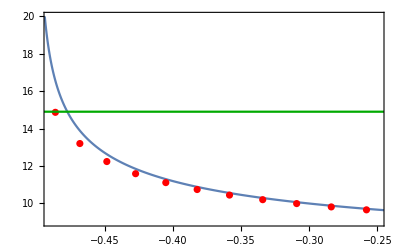

```mathematica
Tc=Show[ListPlot[rho1,Joined->True,GridLines->{{},{}},GridLinesStyle->{{Dashed,Thick},{}},PlotRange->{{-0.49,-0.25},{20,9}},GridLinesStyle->Red,Frame->True,LabelStyle->{15,Black}],ListPlot[{dataT},PlotStyle->Red],Plot[14.9,{x,-0.5,-0.2},PlotStyle->{Darker[Green]}],Axes->False]
```

#### Third Column

```mathematica
g=2^(1/2);
rho1={};
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,4}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
qtp3=qtpsort[[3]];
qtp4=qtpsort[[4]];
rhoinst1=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
rhoinst2=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp3,qtp4}];
AppendTo[rho1,{en,Re[rhoinst1]+Re[rhoinst2]}],{en,-0.625,-0.5005,0.001}];
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,2}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
rhoinst1=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
AppendTo[rho1,{en,Re[rhoinst1]}],{en,-0.4995,-0.2,0.001}];
```

```mathematica
datarho={{-30.891219305606537, 1.1695581680077685},
{-30.04260636181629, 1.1873633947991613},
{-29.208146602107433, 1.2096032247387658},
{-28.391090381025087, 1.2385510363574008},
{-27.59651813942441, 1.2791822832122397},
{-26.83507863412209, 1.3492916815959293},
{-26.139603353463514, 1.538885407927282},
{-25.54456999623379, 1.8510094712153373},
{-24.95239642737438, 1.552550606222522},
{-24.24517513209946, 1.2981260723802746},
{-23.44078284759713, 1.192686399967416},
{-22.578109960689982, 1.127519771516704},
{-21.67119809397417, 1.0788402123847443},
{-20.726930330269944, 1.0399180860026467},
{-19.74992925719839, 1.0076704432958266},
{-18.743692741111108, 0.9803103801102522},
{-17.711012369128973, 0.9566854388511927},
{-16.65418874361456, 0.9360039193903286},
{-15.57516091553309, 0.9176971889017521},
{-14.475590926826523, 0.9013427082840794},
{-13.356921990084446, 0.8866176050747027},
{-12.220418561687309, 0.8732671874047547},
{-11.067183965099606, 0.861071092556607},
{-9.898107357235038 ,0.8497556242712736},
{-8.713536923041564 ,0.8386926164900954},
{-7.512133158602792 ,0.8261215795035435},
{-6.288283790596326, 0.8082616276609726},
{-5.029196292886644, 0.7806694736220358},
{-3.7156384812107106, 0.7428516601282767},
{-2.3279186876507234, 0.6996550254120536},
{-0.8516994442146141, 0.6565286900820524}};
dataT=Table[{datarho[[i,1]]/R,4π*datarho[[i,2]]},{i,1,Length[datarho]}];
```

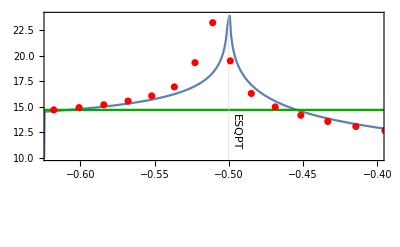

```mathematica
Tc=Show[ListPlot[rho1,Joined->True,GridLines->{{-.5},{}},GridLinesStyle->{{Dashed,Thick},{}},PlotRange->{{-0.62,-0.4},{10,24}},GridLinesStyle->Red,Frame->True,LabelStyle->{15,Black},Epilog->{Inset[Rotate[Text[Style["ESQPT",Black,14]],-90 Degree],{-0.495,12.5}],Inset[Rotate[Text[Style["ESQPT",Black,14]],-90 Degree],{-0.575,4.0}]}],Plot[14.7,{x,-0.625,-0.35},PlotStyle->{Darker[Green]}],ListPlot[{dataT},PlotStyle->Red],Axes->False]
```

#### Fourth Column

```mathematica
g=2;
rho1={};
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,4}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
qtp3=qtpsort[[3]];
qtp4=qtpsort[[4]];
rhoinst1=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
rhoinst2=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp3,qtp4}];
AppendTo[rho1,{en,Re[rhoinst1]+Re[rhoinst2]}],{en,-1.05,-0.5005,0.001}];
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,2}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
rhoinst1=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
AppendTo[rho1,{en,Re[rhoinst1]}],{en,-0.4995,-0.2,0.001}];
```

```mathematica
datarho={{-52.65744059872463,1.033899661890845},{-51.69077266916237,1.035063807397849},{-50.72522477180006,1.0362997339666449},{-49.76086418269499,1.0376141380313815},{-48.797764285076276,1.0390145840088376},{-47.836005341098016,1.0405096525929425},{-46.875675392672875,1.0421091212506064},{-45.916871318973605,1.0438241855676083},{-44.95970008552635,1.0456677329113444},{-44.00428022953735,1.0476546837939618},{-43.05074363912337,1.049802421834847},{-42.09923770180578,1.0521313411010307},{-41.149927922002455,1.0546655510867606},{-40.20300114135195,1.0574337965465754},{-39.25866954415664,1.0604706748571215},{-38.317175699785196,1.0638182715679751},{-37.37879899248719,1.0675283878299053},{-36.44386391660427,1.071665586513551},{-35.51275082135537,1.0763112443475231},{-34.58590953629165,1.081568322170682},{-33.66387514765498,1.0875647480918536},{-32.747281381490254,1.0944486805687665},{-31.83685884935374,1.1023620103868748},{-30.9333971839319,1.1113823948873196},{-30.03767069559675,1.1214877853911907},{-29.15046154153787,1.1328291511918271},{-28.273252368725146,1.1472195923333393},{-27.411425556242236,1.173735198952484},{-26.58418455658336,1.2461042501534354},{-25.82404690513316,1.393195744263958},{-25.095434901843035,1.3523568863891688},{-24.29280034042861,1.154975349615663},{-23.37911519917151,1.0399865055085324},{-22.383120062120433,0.9704598466665239},{-21.322725069229712,0.9171361526564742},{-20.20397097951612,0.8717198590163457},{-19.029023184319527,0.8314362309003422},{-17.79870350008757,0.7949749267902301},{-16.513186537928785,0.7615377055956707},{-15.172224853045828,0.7305718552658225},{-13.775243822521338,0.7016700339517116},{-12.321391130509618,0.6745207520717951},{-10.809564841400334,0.6488793682261471},{-9.238428558972306,0.6245495191603186},{-7.606417487564348,0.6013706150207437},{-5.911737383302632,0.5792091278667443},{-4.1523574627920805,0.5579523600169612},{-2.325997771081838,0.5375038844909199},{-0.43011110544244396,0.5177801401492589}};
dataT=Table[{datarho[[i,1]]/R,4π*datarho[[i,2]]},{i,1,Length[datarho]}];
```

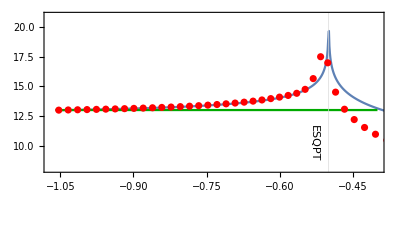

```mathematica
Tc=Show[ListPlot[rho1,Joined->True,GridLines->{{-.5},{}},GridLinesStyle->{{Dashed,Thick},{}},PlotRange->{{-1.07,-0.4},{8,21}},GridLinesStyle->Red,Frame->True,LabelStyle->{15,Black},Epilog->{Inset[Rotate[Text[Style["ESQPT",Black,14]],-90 Degree],{-0.53,10.2}],Inset[Rotate[Text[Style["ESQPT",Black,14]],-90 Degree],{-0.575,4.0}]}],Plot[13,{x,-1.06,-0.4},PlotStyle->{Darker[Green]}],ListPlot[{dataT},PlotStyle->Red],Axes->False]
```

```mathematica
Export["Period_QRM_resonant4.png",Tc]
```

Period_QRM_resonant4.png